```mathematica
Table[NumberOfSpanningTrees[allGraphs5[k,"graph"]],{k,Keys[allGraphs5]}]//Tally//Sort
```

Det::matsq: Argument {} at position 1 is not a non-empty square matrix.

{{0,671},{1,375},{3,295},{4,90},{5,12},{8,180},{9,15},{11,60},{12,10},{16,30},{20,10},{21,60},{24,30},{40,30},{45,15},{75,10},{125,1},{Det[{}],1}}

```mathematica
Select[Keys[allGraphs5],NumberOfSpanningTrees[allGraphs5[#,"graph"]]==125&]
```

Det::matsq: Argument {} at position 1 is not a non-empty square matrix.

{29524}

```mathematica
ShowGraph5Least[29524]
```

-Graphics-295240

```mathematica
TreeCycles[g_]:=Block[{a=AdjacencyMatrix[g]},1/6*Tr[MatrixPower[a,3]]]
```

```mathematica
TreeCycles[allGraphs5[K5Key,"graph"]]
```

10

```mathematica
With[
{mat=AdjacencyMatrix[CompleteGraph[5]]},
Table[MatrixForm[MatrixPower[mat,n]],{n,1,5}]
]
```

{(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0),(4 | 3 | 3 | 3 | 3
3 | 4 | 3 | 3 | 3
3 | 3 | 4 | 3 | 3
3 | 3 | 3 | 4 | 3
3 | 3 | 3 | 3 | 4),(12 | 13 | 13 | 13 | 13
13 | 12 | 13 | 13 | 13
13 | 13 | 12 | 13 | 13
13 | 13 | 13 | 12 | 13
13 | 13 | 13 | 13 | 12),(52 | 51 | 51 | 51 | 51
51 | 52 | 51 | 51 | 51
51 | 51 | 52 | 51 | 51
51 | 51 | 51 | 52 | 51
51 | 51 | 51 | 51 | 52),(204 | 205 | 205 | 205 | 205
205 | 204 | 205 | 205 | 205
205 | 205 | 204 | 205 | 205
205 | 205 | 205 | 204 | 205
205 | 205 | 205 | 205 | 204)}

```mathematica
samples=Flatten[
Table[
Table[
{Prepend[childCouple,k],
{TreeCycles[allGraphs5[k,"graph"]],TreeCycles[allGraphs5[childCouple[[1]],"graph"]],TreeCycles[allGraphs5[childCouple[[2]],"graph"]]},
{allGraphs5[k,"atleast"],allGraphs5[childCouple[[1]],"atleast"],allGraphs5[childCouple[[2]],"atleast"]}
}
,{childCouple,Map[Sort[#,SortByVertexCount]&,allGraphs5[k,"children"]]}],
{k,Keys[allGraphs5]}
],
1]
```

{{{0,19683,39366},{0,0,0},{34,21,13}},{{0,6561,13122},{0,0,0},{34,24,10}},{{0,2187,4374},{0,0,0},{34,24,10}},{{0,729,1458},{0,0,0},{34,21,13}},{{0,243,486},{0,0,0},{34,21,13}},{{0,81,162},{0,0,0},{34,24,10}},{{0,27,54},{0,0,0},{34,24,10}},{{0,9,18},{0,0,0},{34,21,13}},{{0,3,6},{0,0,0},{34,24,10}},{{0,1,2},{0,0,0},{34,21,13}},{{19683,26244,33048},{0,0,0},{21,16,5}},8818,{{1,10,22},{0,0,0},{21,13,8}},{{1,4,16},{0,0,0},{21,16,5}},{{2,19685,39368},{0,0,0},{13,8,5}},{{2,6563,13124},{0,0,0},{13,9,4}},{{2,2918,5834},{0,0,0},{13,8,5}},{{2,2918,5834},{0,0,0},{13,8,5}},{{2,245,488},{0,0,0},{13,8,5}},{{2,110,218},{0,0,0},{13,9,4}},{{2,110,218},{0,0,0},{13,9,4}},{{2,14,26},{0,0,0},{13,8,5}},{{2,14,26},{0,0,0},{13,8,5}}}
 |  |  |  |

```mathematica
SortByVertexCount[k1_,k2_]:=VertexCount[allGraphs5[k1,"graph"]]>VertexCount[allGraphs5[k2,"graph"]]
```

```mathematica
Select[samples,#[[3,1]]==#[[3,2]]+#[[3,3]]&]//Length
```

6700

```mathematica
badPigies1=Select[samples,#[[3,1]]==#[[3,2]]+#[[3,3]]&&#[[3,2]]<#[[3,3]]&&#[[3,2]]≠0&&#[[3,3]]≠0&]
```

{{{29187,29430,29676},{1,2,1},{3,1,2}},{{29187,29196,29205},{1,2,1},{3,1,2}},{{29187,29188,29270},{1,2,1},{3,1,2}},{{28701,29430,30163},{1,2,1},{3,1,2}},{{28701,28710,28800},{1,2,1},{3,1,2}},{{28678,29407,30163},{1,3,1},{3,1,2}},{{28678,28687,28777},{1,3,1},{3,1,2}},{{28948,29677,30406},{0,2,0},{3,1,2}},{{28948,29038,29128},{0,2,0},{3,1,2}},{{28948,29038,29128},{0,2,0},{3,1,2}},430,{{328,337,346},{0,2,0},{7,2,5}},{{120,363,606},{0,2,0},{9,3,6}},{{120,121,122},{0,2,0},{9,3,6}},{{93,336,606},{0,1,0},{11,5,6}},{{93,94,122},{0,1,0},{11,5,6}},{{94,337,607},{1,2,1},{5,2,3}},{{87,97,377},{0,0,0},{5,2,3}},{{87,97,377},{0,0,0},{5,2,3}},{{165,417,697},{0,0,0},{5,2,3}},{{165,417,697},{0,0,0},{5,2,3}}}
 |  |  |  |

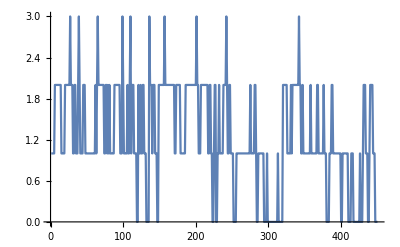

```mathematica
Map[#[[2,2]]-#[[2,3]]&,badPigies1]//ListLinePlot
```

```mathematica
badPigies=Select[samples,#[[3,1]]==#[[3,2]]+#[[3,3]]&&#[[3,2]]>=#[[3,3]]&&#[[3,2]]≠0&&#[[3,3]]≠0&]
```

{{{0,19683,39366},{0,0,0},{34,21,13}},{{0,6561,13122},{0,0,0},{34,24,10}},{{0,2187,4374},{0,0,0},{34,24,10}},{{0,729,1458},{0,0,0},{34,21,13}},{{0,243,486},{0,0,0},{34,21,13}},{{0,81,162},{0,0,0},{34,24,10}},{{0,27,54},{0,0,0},{34,24,10}},{{0,9,18},{0,0,0},{34,21,13}},{{0,3,6},{0,0,0},{34,24,10}},{{0,1,2},{0,0,0},{34,21,13}},{{19683,26244,33048},{0,0,0},{21,16,5}},4768,{{1,10,22},{0,0,0},{21,13,8}},{{1,4,16},{0,0,0},{21,16,5}},{{2,19685,39368},{0,0,0},{13,8,5}},{{2,6563,13124},{0,0,0},{13,9,4}},{{2,2918,5834},{0,0,0},{13,8,5}},{{2,2918,5834},{0,0,0},{13,8,5}},{{2,245,488},{0,0,0},{13,8,5}},{{2,110,218},{0,0,0},{13,9,4}},{{2,110,218},{0,0,0},{13,9,4}},{{2,14,26},{0,0,0},{13,8,5}},{{2,14,26},{0,0,0},{13,8,5}}}
 |  |  |  |

```mathematica
Map[{#[[2,2]]-#[[2,3]],#[[3,2]]-#[[3,3]]}&,badPigies]//Tally//Sort
```

{{{-2,2},20},{{-2,4},10},{{-1,0},20},{{-1,1},105},{{-1,2},130},{{-1,3},45},{{-1,4},35},{{-1,5},20},{{-1,6},5},{{-1,7},5},{{0,0},435},{{0,1},825},{{0,2},560},{{0,3},320},{{0,4},210},{{0,5},80},{{0,6},90},{{0,7},30},{{0,8},40},{{0,9},35},{{0,11},10},{{0,12},10},{{0,14},5},{{1,0},1265},{{1,1},195},{{1,2},130},{{1,3},45},{{2,0},110}}

```mathematica
With[
{prop="atleast"},
Table[
Table[ShowGraph5Least[j,prop]->Map[Labeled[ShowGraph5Least[#,prop],Style[TreeCycles[allGraphs5[#,"graph"]],Blue]]&,Sort[k,VertexCount[allGraphs5[#1,"graph"]]>VertexCount[allGraphs5[#2,"graph"]]&]],{k,
Select[Map[Sort[#,VertexCount[allGraphs5[#1,"graph"]]>VertexCount[allGraphs5[#2,"graph"]]&]&,allGraphs5[j,"children"]],
allGraphs5[#[[1]],prop]-allGraphs5[#[[2]],prop]<0&&allGraphs5[#[[1]],prop]≠0&]}],
{j,Map[First,badies]}
]//Flatten//DeleteDuplicates
]
```

{-Graphics-291873→{-Graphics-2943012,-Graphics-2967621},-Graphics-291873→{-Graphics-2919612,-Graphics-2920521},-Graphics-291873→{-Graphics-2918812,-Graphics-2927021},-Graphics-287013→{-Graphics-2943012,-Graphics-3016321},-Graphics-287013→{-Graphics-2871012,-Graphics-2880021},-Graphics-286783→{-Graphics-2940713,-Graphics-3016321},-Graphics-286783→{-Graphics-2868713,-Graphics-2877721},-Graphics-289483→{-Graphics-2967712,-Graphics-3040620},-Graphics-289483→{-Graphics-2903812,-Graphics-2912820},-Graphics-285423→{-Graphics-2927113,-Graphics-3000121},-Graphics-285423→{-Graphics-2878513,-Graphics-2903721},-Graphics-285163→{-Graphics-2924513,-Graphics-3000121},-Graphics-285163→{-Graphics-2852513,-Graphics-2877721},-Graphics-284587→{-Graphics-2918731,-Graphics-2992040},-Graphics-284587→{-Graphics-2870131,-Graphics-2894740},-Graphics-284587→{-Graphics-2846731,-Graphics-2847640},-Graphics-284673→{-Graphics-2919612,-Graphics-2992921},-Graphics-284673→{-Graphics-2871012,-Graphics-2903721},-Graphics-284703→{-Graphics-2919913,-Graphics-2992921},-Graphics-284703→{-Graphics-2871313,-Graphics-2903721},-Graphics-284803→{-Graphics-2920912,-Graphics-2993820},-Graphics-284803→{-Graphics-2880412,-Graphics-2912820},-Graphics-284616→{-Graphics-2919022,-Graphics-2992040},-Graphics-284616→{-Graphics-2870422,-Graphics-2894740},-Graphics-284625→{-Graphics-2919113,-Graphics-2992040},-Graphics-284625→{-Graphics-2870522,-Graphics-2894830},-Graphics-284625→{-Graphics-2847122,-Graphics-2848030},-Graphics-284595→{-Graphics-2918812,-Graphics-2992040},-Graphics-284595→{-Graphics-2870221,-Graphics-2894830},-Graphics-284595→{-Graphics-2846821,-Graphics-2848030},-Graphics-284356→{-Graphics-2916422,-Graphics-2992040},-Graphics-284356→{-Graphics-2844422,-Graphics-2845340},-Graphics-272973→{-Graphics-2730612,-Graphics-2950221},-Graphics-270813→{-Graphics-2732412,-Graphics-2757921},-Graphics-270813→{-Graphics-2708212,-Graphics-2927021},-Graphics-270634→{-Graphics-2730612,-Graphics-2754930},-Graphics-270643→{-Graphics-2925113,-Graphics-3143820},-Graphics-270643→{-Graphics-2730712,-Graphics-2755020},-Graphics-270573→{-Graphics-2730012,-Graphics-2757921},-Graphics-270005→{-Graphics-2724322,-Graphics-2748931},-Graphics-270093→{-Graphics-2725212,-Graphics-2757921},-Graphics-270013→{-Graphics-2724412,-Graphics-2749021},-Graphics-278223→{-Graphics-3001012,-Graphics-3219820},-Graphics-278223→{-Graphics-2806512,-Graphics-2830820},-Graphics-265685→{-Graphics-2657722,-Graphics-2877331},-Graphics-265953→{-Graphics-2732412,-Graphics-2805621},-Graphics-265953→{-Graphics-2660412,-Graphics-2880021},-Graphics-265953→{-Graphics-2659612,-Graphics-2659721},-Graphics-265713→{-Graphics-2730012,-Graphics-2805621},-Graphics-265713→{-Graphics-2658012,-Graphics-2877721},-Graphics-265693→{-Graphics-2657812,-Graphics-2877721},-Graphics-265145→{-Graphics-2724322,-Graphics-2797531},-Graphics-265233→{-Graphics-2725212,-Graphics-2798421},-Graphics-265153→{-Graphics-2724412,-Graphics-3016321},-Graphics-263527→{-Graphics-2708131,-Graphics-2781340},-Graphics-263527→{-Graphics-2659531,-Graphics-2685040},-Graphics-263527→{-Graphics-2635331,-Graphics-2635440},-Graphics-263615→{-Graphics-2709021,-Graphics-2782230},-Graphics-263615→{-Graphics-2660412,-Graphics-2685040},-Graphics-263615→{-Graphics-2636221,-Graphics-2636630},-Graphics-263645→{-Graphics-2709322,-Graphics-2782230},-Graphics-263645→{-Graphics-2660713,-Graphics-2685040},-Graphics-263645→{-Graphics-2636522,-Graphics-2636630},-Graphics-263663→{-Graphics-2928212,-Graphics-3219820},-Graphics-263663→{-Graphics-2660912,-Graphics-2685220},-Graphics-263556→{-Graphics-2708422,-Graphics-2781340},-Graphics-263556→{-Graphics-2659822,-Graphics-2685040},-Graphics-263563→{-Graphics-2708513,-Graphics-3000121},-Graphics-263563→{-Graphics-2659913,-Graphics-2685121},-Graphics-263533→{-Graphics-2708212,-Graphics-3000121},-Graphics-263533→{-Graphics-2659612,-Graphics-2685121},-Graphics-263347→{-Graphics-2852132,-Graphics-3070840},262,-Graphics-29445→{-Graphics-2262722,-Graphics-4239131},-Graphics-29287→{-Graphics-948932,-Graphics-1605040},-Graphics-29287→{-Graphics-292922,-Graphics-293050},-Graphics-29205→{-Graphics-292922,-Graphics-949931},-Graphics-25233→{-Graphics-2220612,-Graphics-4845021},-Graphics-25233→{-Graphics-252412,-Graphics-328121},-Graphics-25147→{-Graphics-2219731,-Graphics-4844140},-Graphics-25147→{-Graphics-252331,-Graphics-909440},-Graphics-25155→{-Graphics-2219821,-Graphics-4844230},-Graphics-25155→{-Graphics-324421,-Graphics-1053430},-Graphics-25155→{-Graphics-252412,-Graphics-909440},-Graphics-24693→{-Graphics-247012,-Graphics-328121},-Graphics-24613→{-Graphics-319012,-Graphics-3016321},-Graphics-24613→{-Graphics-247012,-Graphics-912121},-Graphics-24633→{-Graphics-247310,-Graphics-985420},-Graphics-24873→{-Graphics-2289910,-Graphics-4995420},-Graphics-24433→{-Graphics-317212,-Graphics-1046221},-Graphics-24347→{-Graphics-316331,-Graphics-1045340},-Graphics-24347→{-Graphics-244331,-Graphics-909440},-Graphics-23076→{-Graphics-255022,-Graphics-279340},-Graphics-23076→{-Graphics-230822,-Graphics-303840},-Graphics-22807→{-Graphics-2196331,-Graphics-4164640},-Graphics-22807→{-Graphics-252331,-Graphics-279340},-Graphics-22807→{-Graphics-228131,-Graphics-303840},-Graphics-22813→{-Graphics-2196412,-Graphics-4164721},-Graphics-22813→{-Graphics-301012,-Graphics-1030021},-Graphics-22813→{-Graphics-252412,-Graphics-279421},-Graphics-227111→{-Graphics-2195451,-Graphics-4163760},-Graphics-22727→{-Graphics-2195531,-Graphics-4163840},-Graphics-22727→{-Graphics-300131,-Graphics-1029140},-Graphics-22727→{-Graphics-228131,-Graphics-909440},-Graphics-22743→{-Graphics-2195711,-Graphics-4164020},-Graphics-22743→{-Graphics-228410,-Graphics-985420},-Graphics-22267→{-Graphics-246931,-Graphics-279340},-Graphics-22267→{-Graphics-222731,-Graphics-303840},-Graphics-22273→{-Graphics-295612,-Graphics-2992921},-Graphics-22273→{-Graphics-247012,-Graphics-279421},-Graphics-221711→{-Graphics-246051,-Graphics-270360},-Graphics-22187→{-Graphics-294731,-Graphics-2992040},-Graphics-22187→{-Graphics-246131,-Graphics-270440},-Graphics-22187→{-Graphics-222731,-Graphics-879740},-Graphics-22415→{-Graphics-2265320,-Graphics-4314730},-Graphics-22503→{-Graphics-2266210,-Graphics-4315620},-Graphics-22005→{-Graphics-292922,-Graphics-1021931},-Graphics-219111→{-Graphics-292051,-Graphics-1021060},-Graphics-219111→{-Graphics-220051,-Graphics-877060},-Graphics-21935→{-Graphics-220320,-Graphics-950330},-Graphics-46443→{-Graphics-537410,-Graphics-2586820},-Graphics-46203→{-Graphics-535010,-Graphics-1265020},-Graphics-44015→{-Graphics-513120,-Graphics-2562530},-Graphics-44043→{-Graphics-513410,-Graphics-3219820},-Graphics-44043→{-Graphics-464711,-Graphics-489020},-Graphics-43775→{-Graphics-510720,-Graphics-1240730},-Graphics-10653→{-Graphics-106612,-Graphics-328121},-Graphics-10574→{-Graphics-106612,-Graphics-107530},-Graphics-8496→{-Graphics-109222,-Graphics-133540},-Graphics-8496→{-Graphics-85022,-Graphics-303840},-Graphics-8227→{-Graphics-106531,-Graphics-133540},-Graphics-8227→{-Graphics-82331,-Graphics-303840},-Graphics-8233→{-Graphics-106612,-Graphics-133621},-Graphics-8943→{-Graphics-114610,-Graphics-142620},-Graphics-3365→{-Graphics-33722,-Graphics-36531},-Graphics-3287→{-Graphics-35532,-Graphics-38240},-Graphics-3287→{-Graphics-33722,-Graphics-34650},-Graphics-1209→{-Graphics-36332,-Graphics-60660},-Graphics-1209→{-Graphics-12132,-Graphics-12260},-Graphics-9311→{-Graphics-33651,-Graphics-60660},-Graphics-9311→{-Graphics-9451,-Graphics-12260},-Graphics-945→{-Graphics-33722,-Graphics-60731},-Graphics-875→{-Graphics-9720,-Graphics-37730},-Graphics-1655→{-Graphics-41720,-Graphics-69730}}
 |  |  |  |